```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{2,4,3,4,4,4,6,0,3,1,31},{2,4,3,2,4,0,2,2,1,1,21},{2,4,3,4,4,3,6,2,2,3,33},{2,3,3,2,0,3,4,0,2,1,20},{1,3,3,4,4,3,3,2,3,3,29},{1,4,3,4,1,4,4,2,3,0,26},{3,4,3,4,3,4,4,2,1,3,31},{3,2,3,4,4,3,6,1,1,3,30},{2,4,3,4,4,2,3,2,3,1,28},{2,3,3,0,0,0,0,0,0,0,8},{1,3,3,4,4,3,3,0,1,0,22},{3,4,3,4,4,4,5,2,3,3,35},{2,0,0,0,0,0,0,1,0,0,3},{1,3,3,4,4,3,4,2,2,1,27},{2,4,3,2,2,3,3,0,1,1,21},{3,4,3,4,4,4,5,2,3,3,35},{2,1,2,2,3,3,5,1,2,3,24},{2,4,3,2,1,4,4,2,2,2,26},{3,4,3,4,4,3,6,2,0,0,29},{3,4,3,4,3,3,3,0,2,1,26},{2,4,3,1,2,1,0,1,0,2,16},{2,4,3,4,3,4,3,2,2,3,30},{1,0,1,1,0,0,0,0,0,0,3},{3,4,3,4,4,4,5,2,2,3,34},{1,3,3,4,4,4,3,1,1,2,26},{1,4,1,4,0,2,2,2,2,3,21},{2,0,2,1,2,0,0,2,0,0,9},{2,4,3,1,1,4,4,0,2,2,23},{3,4,3,4,2,4,5,2,3,2,32},{3,4,3,4,3,3,6,2,0,3,31},{3,4,3,4,4,3,4,2,0,0,27},{3,4,3,4,4,4,4,2,3,2,33},{2,4,3,2,4,3,5,0,0,0,23},{1,1,3,2,4,4,4,2,1,3,25}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

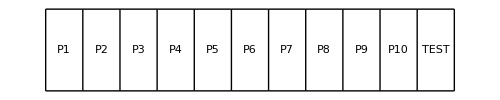
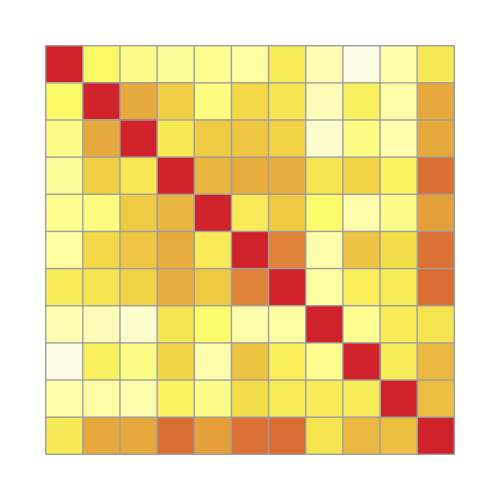
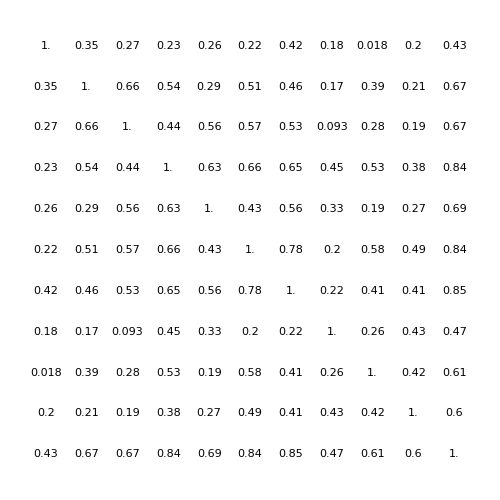
-Graphics-
-Graphics--Graphics--Graphics-

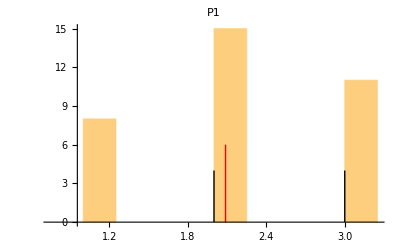
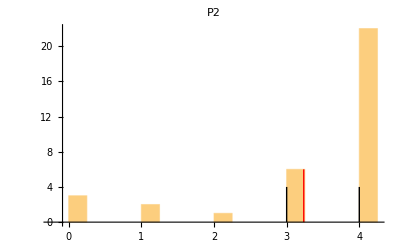
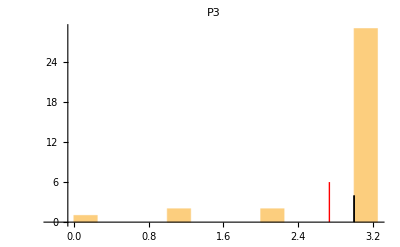
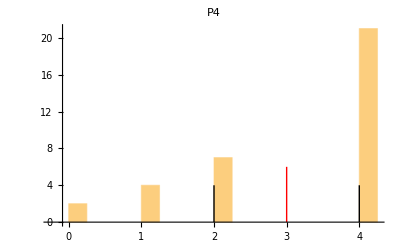
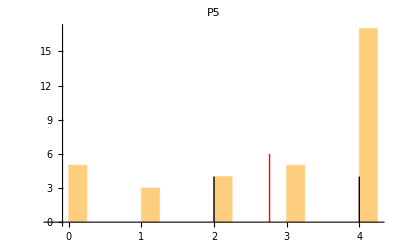
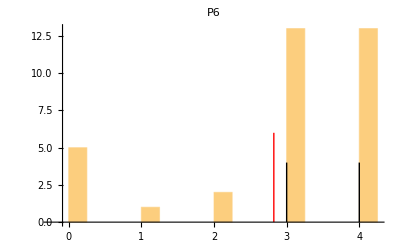
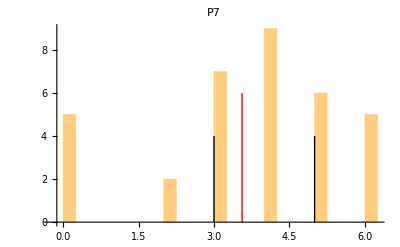
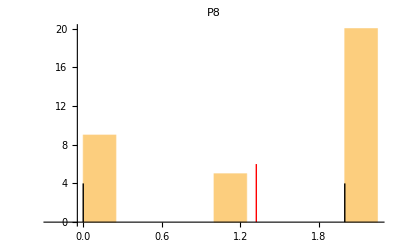

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->46,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],6}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],4}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],4}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```

```mathematica
(*range of scores: 20 to 37*)
(*this is where we'll draw the D to A range (traditionally: 60 to 100)*)
```

```mathematica
Export["test.png",histograms[[11]]]
```

test.png